# Kick-drum

-Graphics-

Principe : on envoie une pulse de 0 à 3.3V sur l'entrée trig et le filtre résonant high-Q génère une sinusoïde amortie. On somme deux sinusoïdes de fréquence et d'amortissement distinct pour simuler un son de kick.

```mathematica
AN={R1->680000.,R2->3300,C1->56 10^-9,C2->56 10^-9,R3->560000,R4->1200,C3->15 10^-9,C4->15 10^-9};
```

## Calcul de la fonction de transfert d'un filtre typique

Les composants sont ceux du premier filtre (R1, R2, C1, C2). L'AOp est en régime linéaire. On note :
- Vm le potentiel sur l'entrée "-" de l'AOp (hypothèse de linéarité : ϵ=0)
- Vs le potentiel sur la sortie de l'AOp
- Vi le potentiel à l'intersection de C1, C2 et R2

```mathematica
eqKirchoff={(Vm-Vi)C1 p+(Vs-Vi)C2 p == Vi/R2,(Vm-Vi)C1 p==(Vs-Vm)/R1};
```

```mathematica
T[p_]=(Vs/.Solve[eqKirchoff,Vs,Vi][[1]]/.Vm->1)//FullSimplify//Together
```

(1+C1 p R1+C1 p R2+C2 p R2+C1 C2 p^2 R1 R2)/(1+C1 p R2+C2 p R2+C1 C2 p^2 R1 R2)

```mathematica
T[p_]=(1+(R1 C1+R2(C1+C2))p+R1 C1 R2 C2 p^2)/(1+R2(C1+C2)p+R1 C1 R2 C2 p^2);
```

```mathematica
TdB[ω_]=20 Log10[Abs[T[ⅈ ω]]];
```

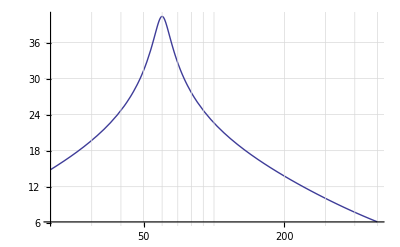

```mathematica
LogLinearPlot[{TdB[ 2 π f]/.AN//Evaluate},{f,20,500},PlotRange->All,GridLines->Automatic]
```

### Propriétés :

Résonance :

```mathematica
ωres = √(1/(R1 R2 C1 C2)); pres=ⅈ ωres;
```

```mathematica
gainResSq=T[pres]T[-pres] // FullSimplify
```

(C2 R2+C1 (R1+R2))^2/((C1+C2)^2 R2^2)

```mathematica
gainRes=(C2 R2+C1 (R1+R2))/((C1+C2) R2);
```

```mathematica
Δω=((C1+C2) (C2 R2+C1 (R1+R2)))/(C1 C2 R1 √(C1^2 R1^2+2 C1 (C1+C2) R1 R2-(C1+C2)^2 R2^2));
```

```mathematica
Q=ωres/Δω//FullSimplify
```

```mathematica
Q=(√(C1 C2))/(C1+C2)√(R1/R2)(√(C1^2 R1^2+2 C1 (C1+C2) R1 R2-(C1+C2)^2 R2^2))/(C2 R2+C1 (R1+R2));
```

A ωres fixé, Q augmente avec R1 :

(0.00002111 R1 √(-1+4.45633×10^-10 R1 (-6600+R1 (2+4.45633×10^-10 (-10890000+6600 R1+R1^2)))))/(1+4.45633×10^-10 R1 (6600+R1+1.47059×10^-6 R1 (3300+R1)))

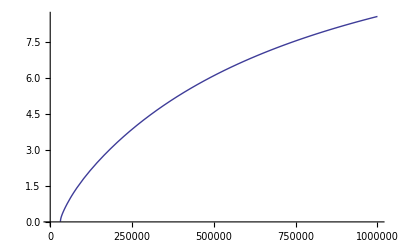

```mathematica
QR1=(R1 √(-1+C1^2 R1 wres^2 (-2 R2+R1 (2+C1^2 (R1^2+2 R1 R2-R2^2) wres^2))) C1 wres)/(1+C1^2 R1 wres^2 (R1+2 R2+C1^2 R1 R2 (R1+R2) wres^2))/.{wres->ωres/.AN,R2->3300,C1->56 10^-9}
Plot[%,{R1, 1000,1000000}]
```

... mais Q diminue lorsque R2 augmente :

(14.3548 √(-1+0.00030303 (-2 R2+680000. (2+4.45633×10^-10 (4.624×10^11+1.36×10^6 R2-R2^2)))))/(1+0.00030303 (680000.+2 R2+0.00030303 R2 (680000.+R2)))

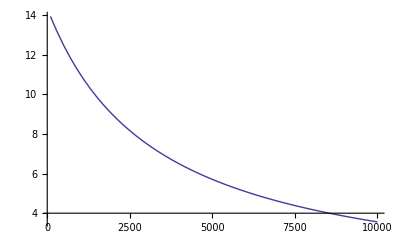

```mathematica
QR1=(R1 √(-1+C1^2 R1 wres^2 (-2 R2+R1 (2+C1^2 (R1^2+2 R1 R2-R2^2) wres^2))) C1 wres)/(1+C1^2 R1 wres^2 (R1+2 R2+C1^2 R1 R2 (R1+R2) wres^2))/.{wres->ωres/.AN,R1->680000.,C1->56 10^-9}
Plot[%,{R2, 100,10000}]
```